```mathematica
(*This is the path that contains the executables and loads SDPB*)
executablesPath = "/home/pano/.local/src/sdpb/build";
<<"/home/pano/.local/src/sdpb/mathematica/SDPB.m";
```

# Gap Consistency Checks

## We constrain possible values for the Gap of a CFT by searching for a functional which breaks everything hehe.

## Defining the Matrix Problem

Let’s first construct the matrix problem and tell SDPB to export the description into a JSON file for SDPB to actually run the thing.

terminateReason = "found primal-dual optimal solution";
primalObjective = 0.1994308448553125017562388947227990310844950542979586431840731710545962923816764033318812556497308054522380528503058110373238065177833468125713544548574299557170951076825267378179490111866198128431348537215499599406604532256912293448350128532067219199789006749465184220591323076461068996622892856895194157940083;
dualObjective   = 0.1994308448553125017562388947222572151338708845416324065550717114872488801867893438061747755958633656404213131014704431908733081451513741047845107946134375744795640835464112272032128521774919309981613958109668656987077555557992150575821581109230935409224056528753262362243112078845473190175899728957195269786452;
dualityGap      = 5.418159506241697563262366290014595673474121948870595257064800538674398118167397488353678464504983726319727077868436602439923812375310241361155106147361590091278818449734579105830942419526976698920142872528547422836283790564950220711921858348210997615595806446993127937998888153630477096049327024032567018826699e-31;
primalError     = 2.676166251196692914870820393720581200817982912791294749256304735138442021433321138310057616525711349436941514462147302678853127644792346906700098194684033218747938465265030902819976494112774550088547792187627431033914916469322061388231908136209022616779195570252426923159801233142248147073072008257346710005092e-251;
dualError       = 6.298298828200727023887811720883158307165390911924600190556954830043868152516879220395481990446422647718735779463962973288709724595491430624853075418966760414478738521081858930127827504978521081959814260283594139888894968165998117259712045288465664460931349200154746816821616889567141633948585203000204050460989e-266;
Solver runtime  = 13;

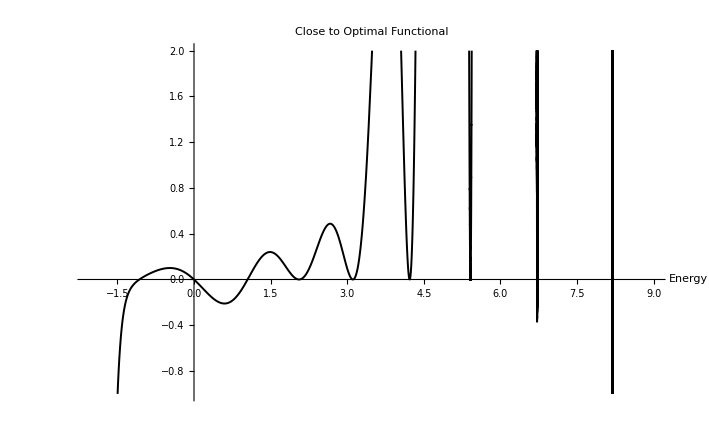

```mathematica
(*Precision and directories*)
precision = 1024;
file ="/home/pano/projects/sdpb-test/pmp.json";
sdpdir="/home/pano/projects/sdpb-test/sdp";
outdir="/home/pano/projects/sdpb-test/out";
outfile ="/home/pano/projects/sdpb-test/out/z.txt";
Run[StringRiffle[{
"rm -rf",
FileNameJoin[{sdpdir,"*"}],
sdpdir<>".ck",
FileNameJoin[{outdir,"*"}]
}]];

(*Maximum order of derivatives in the linear functional a*)
P=35; 

(*Central charge*)
c = 12; 

(*Threshold*)
threshold=1; 

(*Gap energy*)
E0=1+ 0.05; 

(*Polynomial generator function*)
poly[n_,E0_,x_]:=Sum[StirlingS2[n,k](-2π (x+E0))^k,{k,1,n}]; 

(*Construct a module that does this whole sdpb definition thingy*)
solve[gapEnergy_:E0,centralCharge_:c, order_:P, precision_:precision,thresh_:threshold]:=
Module[{
E0=gapEnergy,
c=centralCharge,
NN=Floor[order/2],
threshold=thresh,
objective,
normalization,
matrices
},

(*Objective vector*)
(*objective = {0}~Join~(poly[2#+1,0,-c/12]&/@Range[0,NN]);*)
objective = (poly[2#+1,0,-c/12]&/@Range[0,NN]);
(*objective = {0}~Join~(-(poly[2#+1,0,-c/12]&/@Range[0,NN]));*)

(*Normalization vector*)
(*normalization = {1}~Join~(Range[0,NN]*0);*)
normalization = (poly[2#+1,0,-c/(12*2)]&/@Range[0,NN])*threshold;
(*normalization = {1}~Join~(Range[0,NN]*0);*)

(*Polynomial list*)
matrices={
PositiveMatrixWithPrefactor[<|
(*"polynomials"->{{{0}~Join~(Expand[poly[2#+1,E0,x],x]&/@Range[0,NN])}}*)
"polynomials"->{{(Expand[poly[2#+1,E0,x],x]&/@Range[0,NN])}}
(*"polynomials"->{{{0}~Join~(Expand[poly[2#+1,E0,x],x]&/@Range[0,NN])}}*)
|>]
(*,PositiveMatrixWithPrefactor[<|
"prefactor"-> 1,
"polynomials"->{{{-threshold}~Join~(poly[2#+1,0,-c/12]&/@Range[0,NN])}}
|>]*)
};

(*Define SDP*)
WritePmpJson[file, SDP[objective,normalization,matrices], precision];

(*Run the magical code to solve*)
Run[StringRiffle[{
FileNameJoin[{executablesPath,"pmp2sdp"}],
ToString[precision], file, sdpdir
}]];
Run[StringRiffle[{
"mpirun"
,FileNameJoin[{executablesPath,"sdpb"}]
,"-s", sdpdir, "-o", outdir
,"--precision="<> ToString[precision]
,"--noFinalCheckpoint"
,"--maxIterations="<>ToString[5000]
,"--dualityGapThreshold=1e-30"
, "--writeSolution=\"x,y,z\""
,"--maxComplementarity=1e+100"
(*,"--findDualFeasible"*)
}]];
(*ToExpression@Import[FileNameJoin[{outdir,"out.txt"}],"Text"];*)
fullResult = Import[FileNameJoin[{outdir,"out.txt"}], "String"];
Echo[fullResult];
];
solve[]
(* Get the optimal vector *)
α=(Import[outfile,"Table"][[2;;]]//Flatten).(poly[2#+1,0,x]&/@Range[0,Floor[P/2]])//Simplify;
Plot[α/threshold/10,{x,-c/12-E0,9},PlotRange->{-1,2} ,MaxRecursion->15,AxesLabel->{HoldForm[Energy],None},PlotLabel->HoldForm[Close to Optimal Functional],LabelStyle->{8},PlotStyle->{Black,Thickness[0.002]}]
```

{0.199431,0.,-0.393487,0.0708343,0.951867}

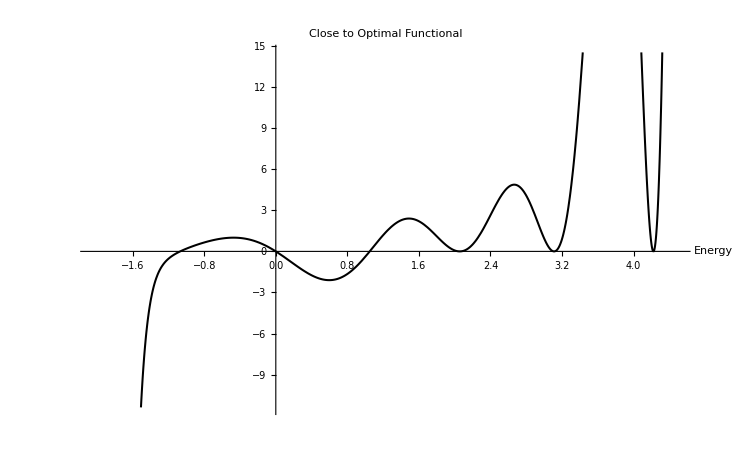

```mathematica
α=(Import[outfile,"Table"][[2;;]]//Flatten).(poly[2#+1,0,x]&/@Range[0,Floor[P/2]])//Simplify;
Echo[N[(α/threshold)/.x->(#)]& /@{-1,0,1,2,3}];
Plot[α/threshold,{x,-c/12-E0,4.5},MaxRecursion->15,AxesLabel->{HoldForm[Energy],None},PlotLabel->HoldForm[Close to Optimal Functional],LabelStyle->{8},PlotStyle->{Black,Thickness[0.002]}]
```

```mathematica
(α/.x->(-1))
```

-9.9999999999850799779390888398753732149340492500125376305015566090340266685713218845609710325723995072375847844725178751100828040997272175691606680431230730650163853521765658120162805612621258348408691687117528526808865304737902665703244479149105501636218224173678052771034890952889214281076595754262702×10^-21

```mathematica
StringRiffle[{
"rm -rf",
FileNameJoin[{sdpdir,"*"}],
sdpdir<>".ck",
FileNameJoin[{outdir,"*"}],
"&&",
FileNameJoin[{executablesPath,"pmp2sdp"}],
ToString[precision], file, sdpdir,
 "&&",
"mpirun",
FileNameJoin[{executablesPath,"sdpb"}],
"-s", sdpdir, "-o", outdir,
"--precision="<> ToString[precision],
"--noFinalCheckpoint"
,"--maxIterations="<>ToString[5000]
,"--dualityGapThreshold=1e-10"
, "--writeSolution=\"x,y,z\""
}]//CopyToClipboard
```

```mathematica
poly[7,0,x/(-2Pi)]
```

x+63 x^2+301 x^3+350 x^4+140 x^5+21 x^6+x^7

```mathematica
(α)/threshold//N//Expand
```

-20.9169 x-17.4548 x^2+25.1191 x^3+28.8852 x^4-0.0107088 x^5-13.204 x^6-5.66804 x^7+1.19877 x^8+1.96292 x^9+0.3976 x^10-0.100634 x^11-0.183745 x^12+0.0305163 x^13-0.0390647 x^14+0.0487582 x^15-0.0379898 x^16+0.032086 x^17-0.0252429 x^18+0.017666 x^19-0.0110966 x^20+0.00613441 x^21-0.00294409 x^22+0.00121635 x^23-0.00042819 x^24+0.000127052 x^25-0.0000314153 x^26+6.38507×10^-6 x^27-1.04914×10^-6 x^28+1.36714×10^-7 x^29-1.38183×10^-8 x^30+1.05372×10^-9 x^31-5.83214×10^-11 x^32+2.20368×10^-12 x^33-5.07244×10^-14 x^34+5.35648×10^-16 x^35